# Name - Vinay Kishor Roll no. - 20201459 Course - B.Sc (H) computer science Secant method in different forms:-

### Secant method: for given parameters

x0 = 1

x1 = 2

Nmax = 20

epsilon = 1/1000000

f[x] := Cos[x]

In1th number of iterations the root is :1.5649

Estimated error is :0.435096

In2th number of iterations the root is :1.57098

Estimated error is :0.0060742

In3th number of iterations the root is :1.5708

Estimated error is :0.000182249

1.5708

Root is :1.5708

Estimated error is :1.02185×10^-9

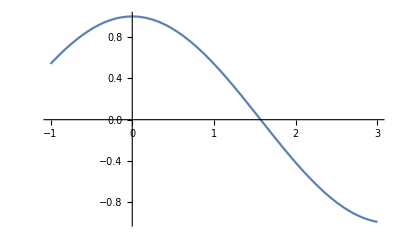

```mathematica
x0 = Input["Enter first number :"];
x1 = Input["Enter second number :"];
Nmax =Input["Enter maximum number of iterations :"];
eps = Input["Enter a value of convergence parameter :"];
Print["x0 = ",x0];
Print["x1 = ",x1];
Print["Nmax = ",Nmax];
Print["epsilon = ",eps];
f[x_] := Cos[x];
Print["f[x] := ",f[x]];
For[i =1 , i≤ Nmax, i++,
x2 = 
N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x]/.x->x0))];
If[Abs[x1-x2]<eps,Return[x2],x0 = x1;x1 = x2];
Print["In",i,"th number of iterations the root is :",x2];
Print["Estimated error is :",Abs[x1-x0]]];
Print["Root is :",x2];
Print["Estimated error is :",Abs[x2-x1]];
Plot[f[x],{x,-1,3}]
```

x0 = 0

x1 = 1

Nmax = 20

epsilon = 1/1000000

f[x] := 1-5 x+x^3

In1th number of iterations the root is :0.25

Estimated error is :0.75

In2th number of iterations the root is :0.186441

Estimated error is :0.0635593

In3th number of iterations the root is :0.201736

Estimated error is :0.0152956

In4th number of iterations the root is :0.20164

Estimated error is :0.0000964033

0.20164

Root is :0.20164

Estimated error is :1.7717×10^-7

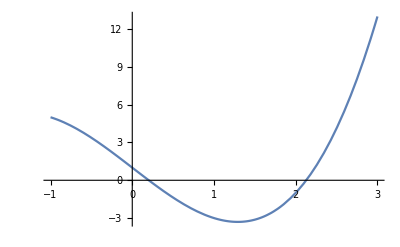

```mathematica
x0 = Input["Enter first number :"];
x1 = Input["Enter second number :"];
Nmax =Input["Enter maximum number of iterations :"];
eps = Input["Enter a value of convergence parameter :"];
Print["x0 = ",x0];
Print["x1 = ",x1];
Print["Nmax = ",Nmax];
Print["epsilon = ",eps];
f[x_] := x^3 -5x +1;
Print["f[x] := ",f[x]];
For[i =1 , i≤ Nmax, i++,
x2 = 
N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x]/.x->x0))];
If[Abs[x1-x2]<eps,Return[x2],x0 = x1;x1 = x2];
Print["In",i,"th number of iterations the root is :",x2];
Print["Estimated error is :",Abs[x1-x0]]];
Print["Root is :",x2];
Print["Estimated error is :",Abs[x2-x1]];
Plot[f[x],{x,-1,3}]
```

x0 = 0

x1 = 1

Nmax = 20

epsilon = 1/1000000

f[x] := -ⅇ^x x+Cos[x]

In1th number of iterations the root is :0.314665

Estimated error is :0.685335

In2th number of iterations the root is :0.446728

Estimated error is :0.132063

In3th number of iterations the root is :0.531706

Estimated error is :0.0849777

In4th number of iterations the root is :0.516904

Estimated error is :0.0148014

In5th number of iterations the root is :0.517747

Estimated error is :0.000842998

In6th number of iterations the root is :0.517757

Estimated error is :9.90548×10^-6

0.517757

Root is :0.517757

Estimated error is :7.07182×10^-9

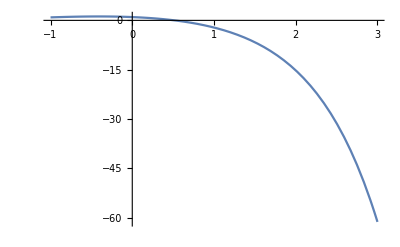

```mathematica
x0 = Input["Enter first number :"];
x1 = Input["Enter second number :"];
Nmax =Input["Enter maximum number of iterations :"];
eps = Input["Enter a value of convergence parameter :"];
Print["x0 = ",x0];
Print["x1 = ",x1];
Print["Nmax = ",Nmax];
Print["epsilon = ",eps];
f[x_] := Cos[x]-x*Exp[x];
Print["f[x] := ",f[x]];
For[i =1 , i≤ Nmax, i++,
x2 = 
N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x]/.x->x0))];
If[Abs[x1-x2]<eps,Return[x2],x0 = x1;x1 = x2];
Print["In",i,"th number of iterations the root is :",x2];
Print["Estimated error is :",Abs[x1-x0]]];
Print["Root is :",x2];
Print["Estimated error is :",Abs[x2-x1]];
Plot[f[x],{x,-1,3}]
```